# Generalized QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Resonant_k\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

## Grid

```mathematica
radius=2;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{20069,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{mat, d, idx, matEven, matOdd, esEven, esOdd,
          phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,
          fullVecsEven, fullVecsOdd},
    mat = Floqsym[jParam, alphaParam, kParam];
    d = 2 jParam + 1;
    idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];
    idxE = Ordering[phEven]; idxO = Ordering[phOdd];
    vecsEven = esEven[[2, idxE]];
    vecsOdd  = esOdd[[2, idxO]];
    fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];
    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];
    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ];
```

## Method

```mathematica
(*Floquet parameters*)
J=500;
d=2 J+1;
α=Pi/2.;
k=J*Pi(8/2.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 20069 points...

```mathematica
Print["Computing Floquet matrix..."];
data=GetQKTParityEigensystem[J,α,k];
```

Computing Floquet matrix...

```mathematica
neweigenvec=Join[data["Even","FullVectors"],data["Odd","FullVectors"]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

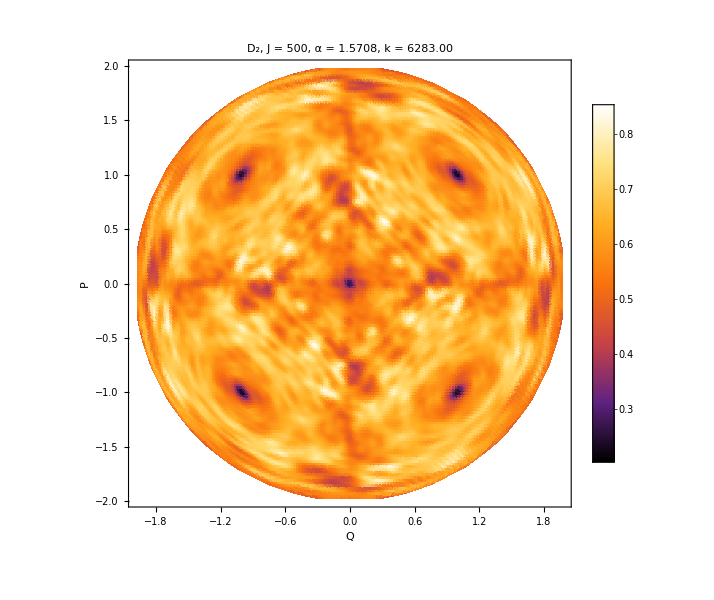

d2_J_500alpha_1.5708_k_6283.19_.png

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
Export["d2_J_"<>ToString[J]<>"alpha_"<>ToString[α]<>"_k_"<>ToString[k]<>"_.png",plot]
```

## Husimis

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,1,2J+1,100}];
```

## Husimis of degenerate groups

```mathematica
(* Operates on a single sector's phase list; returns indices local to that sector *)
GroupStateIndicesSector[phases_, delta_ : 0.01] :=
  Module[{ord, sp, n, breaks, starts, ends, slices},
    ord = Ordering[phases];
    sp  = phases[[ord]];
    n   = Length[sp];
    breaks = Select[Range[n - 1], sp[[# + 1]] - sp[[#]] > delta &];
    starts = Prepend[breaks + 1, 1];
    ends   = Append[breaks, n];
    slices = MapThread[Range, {starts, ends}];
    If[2 Pi - sp[[n]] + sp[[1]] < delta,
      slices = Prepend[slices[[2 ;; -2]], Join[slices[[-1]], slices[[1]]]]];
    ord[[#]] & /@ slices];

(* Splits the merged husimiValues matrix by parity sector *)
SectorHusimiValues[data_, husimiValues_] :=
  Module[{nEven = Length[data["Even"]["FullVectors"]]},
    <|"Even" -> husimiValues[[1 ;; nEven]],
      "Odd"  -> husimiValues[[nEven + 1 ;; All]]|>];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiSectors=SectorHusimiValues[data,husimiValues];
groupIndices=<|"Even"->GroupStateIndicesSector[data["Even"]["Phases"],0.1],"Odd"->GroupStateIndicesSector[data["Odd"]["Phases"],0.1]|>;
```

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
Do[Do[Module[{groupDir},groupDir=FileNameJoin[{dir,sector,"Group_"<>ToString[g]}];
If[!DirectoryQ[groupDir],CreateDirectory[groupDir]];
Do[Module[{idx,husimiList,plot},idx=groupIndices[sector][[g,i]];
husimiList=MapThread[Append,{region,husimiSectors[sector][[idx]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", "<>sector<>" Group "<>ToString[g]<>" ("<>ToString[Length[groupIndices[sector][[g]]]]<>" states)"<>", State "<>ToString[idx],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{groupDir,"Husimi_"<>sector<>"_state_"<>ToString[idx]<>".png"}],plot]],{i,Length[groupIndices[sector][[g]]]}]],{g,Length[groupIndices[sector]]}],{sector,{"Even","Odd"}}];
```

$Aborted

# Sortings

```mathematica
(* ── Quasienergies (both parities, same order as neweigenvec) ── *)
quasienergies = Join[data["Even", "Phases"], data["Odd", "Phases"]];

(* ── Husimi values: rows = eigenstates, cols = phase-space points ── *)
husimi = Abs[overlaps]^2;  (* already normalized per row *)

(* ── 1. IPR of each eigenstate over phase space ── *)
iprEigen = Total[husimi^2, {2}];

(* ── 2. Shannon entropy of each eigenstate ── *)
shannonEntropy = -Total[husimi * Log[husimi + $MachineEpsilon], {2}];
```

```mathematica
(* ── 3. Second moment (variance) of Husimi on phase space ── *)
Q = region[[All, 1]];
P = region[[All, 2]];
meanQ = husimi . Q;
meanP = husimi . P;
meanQ2 = husimi . (Q^2);
meanP2 = husimi . (P^2);
secondMoment = (meanQ2 - meanQ^2) + (meanP2 - meanP^2);
```

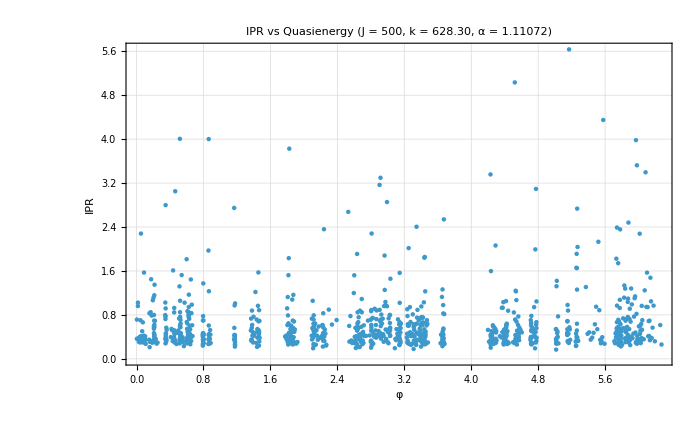

```mathematica
p1 = ListPlot[
  Transpose[{quasienergies, iprEigen}],
  FrameLabel -> {Style["φ", 16], Style["IPR", 16]},  PlotLabel -> Style["IPR vs Quasienergy  (J = " <> ToString[J] <> ", k = " <> ToString[NumberForm[k, {4,2}]] <> ", α = " <> ToString[N[α]] <> ")", 14],PlotTheme->"Detailed",PlotRange->All,ImageSize->700]
```

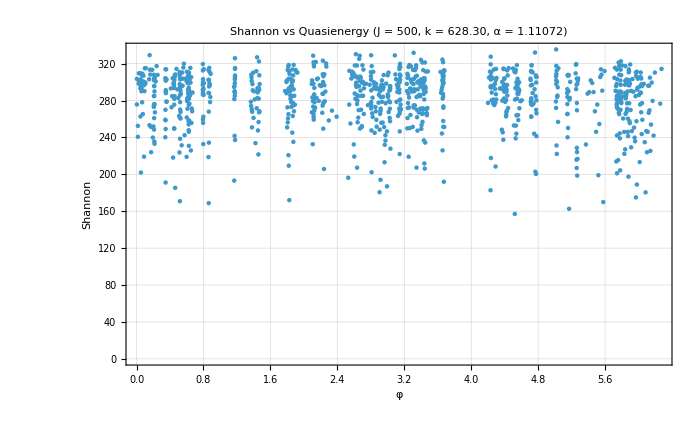

```mathematica
p2 = ListPlot[
  Transpose[{quasienergies, shannonEntropy}],
  FrameLabel -> {Style["φ", 16], Style["Shannon", 16]},  PlotLabel -> Style["Shannon vs Quasienergy  (J = " <> ToString[J] <> ", k = " <> ToString[NumberForm[k, {4,2}]] <> ", α = " <> ToString[N[α]] <> ")", 14],PlotTheme->"Detailed",PlotRange->All,ImageSize->700]
```

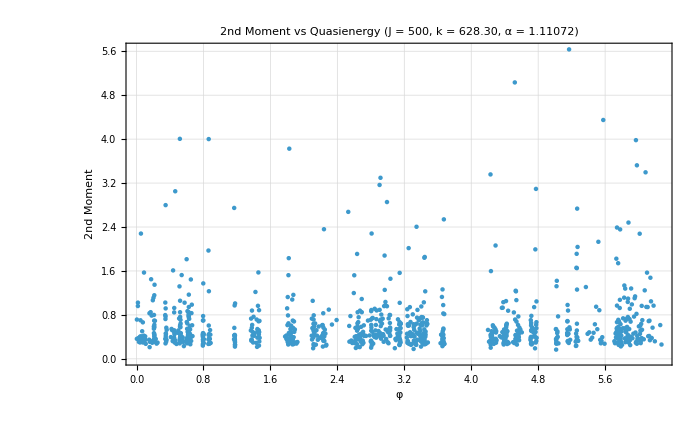

```mathematica
p1 = ListPlot[
  Transpose[{quasienergies, iprEigen}],
  FrameLabel -> {Style["φ", 16], Style["2nd Moment", 16]},  PlotLabel -> Style["2nd Moment vs Quasienergy  (J = " <> ToString[J] <> ", k = " <> ToString[NumberForm[k, {4,2}]] <> ", α = " <> ToString[N[α]] <> ")", 14],PlotTheme->"Detailed",PlotRange->All,ImageSize->700]
```

```mathematica
(* ── Composite localization score (rank each criterion, sum ranks) ── *)
rankIPR     = Ordering[Ordering[-iprEigen]];      (* high IPR = more localized -> rank ascending by -IPR *)
rankEntropy = Ordering[Ordering[shannonEntropy]];  (* low entropy = more localized -> rank ascending *)
rankMoment  = Ordering[Ordering[secondMoment]];   (* low moment = more localized -> rank ascending *)
compositeRank = rankIPR + rankEntropy + rankMoment;
```

```mathematica
nPlot = 50;
sortedIdx = Ordering[compositeRank];
selectedIdx = Take[sortedIdx, nPlot];

dir = "HusimiSorted";
If[!DirectoryQ[dir], CreateDirectory[dir]];

(* ── Distribute shared data to all kernels ── *)
DistributeDefinitions[region, husimi, quasienergies, shannonEntropy, iprEigen, selectedIdx, dir, nPlot];
```

```mathematica
ParallelDo[
  Module[{idx, husimiList, plot, fname},
    idx = selectedIdx[[n]];
    husimiList = MapThread[Append, {region, husimi[[idx]]}];
    plot = ListDensityPlot[husimiList,
      PlotRange -> All,
      PlotTheme -> "Detailed",
      ColorFunction -> "BlueGreenYellow",
      InterpolationOrder -> 1,
      AspectRatio -> 1,
      ImageSize -> 800,
      Frame -> True,
      FrameLabel -> {Style["Q", 30, Black], Rotate[Style["P", 30, Black], -90 Degree]},
      LabelStyle -> Directive[20, Black],
      PlotLabel -> Style[
        "rank=" <> ToString[n] <>
        "  q = " <> ToString[idx] <>
        "  φ = " <> ToString[NumberForm[quasienergies[[idx]], {5,3}]] <>
        "  S = " <> ToString[NumberForm[shannonEntropy[[idx]], {5,3}]] <>
        "  IPR = " <> ToString[NumberForm[iprEigen[[idx]], {4,3}]],
        18, Black]
    ];
    fname = FileNameJoin[{dir,
      "rank" <> IntegerString[n, 10, 3] <>
      "_q" <> ToString[idx] <>
      "_phi" <> ToString[NumberForm[quasienergies[[idx]], {5,3}]] <>
      ".png"}];
    Export[fname, plot];
  ],
  {n, 1, nPlot},
  Method -> "CoarsestGrained"
];
```

## Quasienergies

```mathematica
s = 5;
targets = Table[p * Pi / s, {p, 0, 2s - 1}];

(* wrap distance accounting for 2π periodicity *)
delta = Map[
  Min[Min[Abs[# - targets]], Min[Abs[# - targets - 2Pi]], Min[Abs[# - targets + 2Pi]]] &,
  quasienergies
];
```

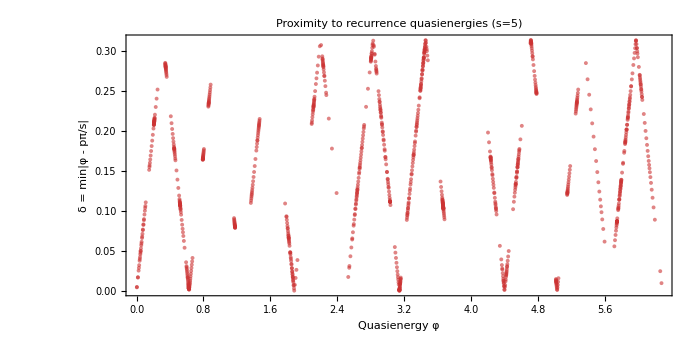

```mathematica
ListPlot[Transpose[{quasienergies,delta}],PlotStyle->Directive[PointSize[0.004],Opacity[0.6],RGBColor[0.8,0.2,0.2]],FrameLabel->{Style["Quasienergy φ",16],Style["δ = min|φ - pπ/s|",16]},PlotLabel->Style["Proximity to recurrence quasienergies  (s="<>ToString[s]<>")",14],LabelStyle->Directive[14,Black],ImageSize->700,AspectRatio->1/2,Frame->True]
```

```mathematica
thresholds={0.005,0.05,0.10,0.15};
Table[{thresh,Count[delta,d_/;d<thresh]},{thresh,thresholds}]//TableForm
```

0.005 | 43
0.05 | 181
0.1 | 288
0.15 | 497

```mathematica
(* ── Select eigenstates with delta < 0.02 (yields 60 states) ── *)
selectedIdx = Flatten[Position[delta, d_ /; d < 0.005]];

nPlot = Length[selectedIdx];  (* should be 60 *)
Print["Selected ", nPlot, " eigenstates with δ < 0.02"];

(* ── Sort selected by delta ascending within the selection ── *)
selectedIdx = selectedIdx[[Ordering[delta[[selectedIdx]]]]];

(* ── Export ── *)
dir = "HusimiDelta002";
If[!DirectoryQ[dir], CreateDirectory[dir]];

DistributeDefinitions[region, husimi, quasienergies, shannonEntropy, iprEigen, delta, selectedIdx, dir, nPlot];
```

Selected 43 eigenstates with δ < 0.02

```mathematica
ParallelDo[
  Module[{idx, husimiList, plot, fname},
    idx = selectedIdx[[n]];
    husimiList = MapThread[Append, {region, husimi[[idx]]}];
    plot = ListDensityPlot[husimiList,
      PlotRange -> All,
      PlotTheme -> "Detailed",
      ColorFunction -> "BlueGreenYellow",
      InterpolationOrder -> 1,
      AspectRatio -> 1,
      ImageSize -> 800,
      Frame -> True,
      FrameLabel -> {Style["Q", 30, Black], Rotate[Style["P", 30, Black], -90 Degree]},
      LabelStyle -> Directive[20, Black],
      PlotLabel -> Style[
        "rank=" <> ToString[n] <>
        "  q=" <> ToString[idx] <>
        "  φ=" <> ToString[NumberForm[quasienergies[[idx]], {5,3}]] <>
        "  δ=" <> ToString[NumberForm[delta[[idx]], {5,4}]] <>
        "  S=" <> ToString[NumberForm[shannonEntropy[[idx]], {5,3}]],
        18, Black]
    ];
    fname = FileNameJoin[{dir,
      "rank" <> IntegerString[n, 10, 3] <>
      "_q" <> ToString[idx] <>
      "_delta" <> ToString[NumberForm[delta[[idx]], {5,4}]] <>
      ".png"}];
    Export[fname, plot];
  ],
  {n, 1, nPlot},
  Method -> "CoarsestGrained"
];
```

# Levels

```mathematica
(* ── Parameters ── *)
J = 50;
(*k = J * Pi * (2/3.);*)
alist = Range[0,2Pi, Pi/1000];
alist//Length
```

2001

```mathematica
DistributeDefinitions[GetQKTParityEigensystem, J, k, alist];
(* ── Parallelized diagonalization over alpha ── *)
resultsphi = ParallelTable[
  Module[{data, eigenvalM, eigenvalm},
    data = GetQKTParityEigensystem[J, a, k];
    {eigenvalM, eigenvalm} = {data["Even", "Quasienergies"], data["Odd", "Quasienergies"]};
    {Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}],
     Transpose[{ConstantArray[a, Length[eigenvalm]], Arg[eigenvalm]}]}
  ],
  {a, alist},
  Method -> "CoarsestGrained"
];
```

```mathematica
{levelsM, levelsm} = Transpose[resultsphi];
test=ListPlot[
  {Flatten[levelsm, 1], Flatten[levelsM, 1]},
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k = ", NumberForm[k, {4,2}]}], 25, Black],
  AspectRatio -> 0.5, ImageSize -> 1000,
  PlotRange -> All
]
Export["levels_J_"<>ToString[J]<>"alpha_"<>ToString[α]<>"_k_"<>ToString[k]<>"_.png",test]
```

levels_J_50alpha_1.5708_k_6283.19_.png

# Levels zoom

```mathematica
(* ── Parameters ── *)
J = 100;
k = J * Pi * (1/3);
alist = Range[3.,3.2,0.00020];
alist//Length
```

1001

```mathematica
DistributeDefinitions[GetQKTParityEigensystem, J, k, alist];
(* ── Parallelized diagonalization over alpha ── *)
resultsphi = ParallelTable[
  Module[{data, eigenvalM, eigenvalm},
    data = GetQKTParityEigensystem[J, a, k];
    {eigenvalM, eigenvalm} = {data["Even", "Quasienergies"], data["Odd", "Quasienergies"]};
    {Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}],
     Transpose[{ConstantArray[a, Length[eigenvalm]], Arg[eigenvalm]}]}
  ],
  {a, alist},
  Method -> "CoarsestGrained"
];
```

```mathematica
{levelsM, levelsm} = Transpose[resultsphi];

test=ListPlot[
  {Flatten[levelsm, 1], Flatten[levelsM, 1]},
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k = ", NumberForm[k, {4,2}]}], 25, Black],
  AspectRatio -> 0.75, ImageSize -> 1000,
  PlotRange -> All
];
```

```mathematica
test
```

-Graphics-

```mathematica
Export["levels5_J_"<>ToString[J]<>"_.png",test]
```

levels5_J_100_.png

```mathematica
Export["levels5b_J_"<>ToString[J]<>"_.png",test]
```

levels5b_J_100_.png

# Hypothesis 1

```mathematica
(* ── Free parameters ── *)
J = 500;
alphaTest = Pi / (2 Sqrt[2.]);
k = J * Pi * (2/5.);
nMax = J;
```

```mathematica
(* ── Build full Floquet matrix ── *)
Fmat =Floqsym[J,α,k] (* your pipeline's (2J+1)-dimensional Floquet unitary *);
identity = IdentityMatrix[Length[Fmat]];
```

```mathematica
(* ── Compute ||F^n - e^{iγ}I|| minimized over γ for each n ── *)
recurrenceNorms =ParallelTable[
  Fn = MatrixPower[Fmat, n];
  gamma = Arg[Tr[Fn] / Length[Fmat]];
  {n, Norm[Fn - Exp[I gamma] * identity, "Frobenius"]},
  {n, 1, nMax}
];
```

$Aborted

n    ||F^n - e^{iγ} I||

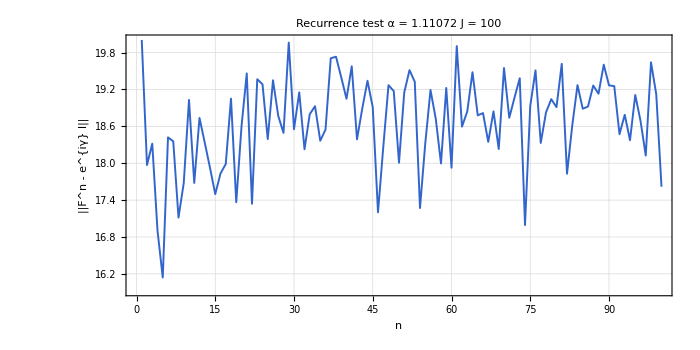

```mathematica
Print["n    ||F^n - e^{iγ} I||"];

ListPlot[recurrenceNorms,
  Joined -> True,
  PlotStyle -> Directive[RGBColor[0.2, 0.4, 0.8], PointSize[0.015], Thickness[0.002]],
  FrameLabel -> {Style["n", 18, Black], Style["||F^n - e^{iγ} I||", 18, Black]},
  PlotLabel -> Style["Recurrence test  α = " <> ToString[NumberForm[alphaTest, {6,5}]] <>
                     "  J = " <> ToString[J], 15, Black],
  Frame -> True, Axes -> False, GridLines -> Automatic,
  ImageSize -> 700, AspectRatio -> 1/2
]
```

# Hypothesis 2

```mathematica
(* ── Free parameters ── *)
J = 100;
alphaCenter = Pi / (2 Sqrt[2]);
k = J * Pi * (2/5.);
alphaRange = 0.1;
alphaStep  = 0.0005;
nTarget    =5;   (* adjust based on Hypothesis 1 output *)
```

```mathematica
(* ── Scan ── *)
alphaList = Range[alphaCenter - alphaRange, alphaCenter + alphaRange, alphaStep];

DistributeDefinitions[GetQKTParityEigensystem, J, k, alphaList, nTarget];
```

```mathematica
scanResults = ParallelTable[
  With[{Fmat = Floqsym[J,α,k]},
    With[{Fn = MatrixPower[Fmat, nTarget]},
      With[{gamma = Arg[Tr[Fn] / Length[Fmat]]},
        {a, Norm[Fn - Exp[I gamma] * IdentityMatrix[Length[Fmat]], "Frobenius"]}
      ]
    ]
  ],
  {a, alphaList},
  Method -> "CoarsestGrained"
];
```

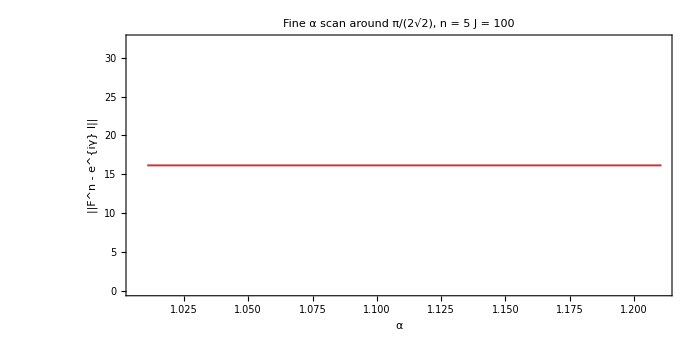

```mathematica
ListPlot[scanResults,
  Joined -> True,
  PlotStyle -> Directive[RGBColor[0.8, 0.2, 0.2], Thickness[0.002]],
  FrameLabel -> {Style["α", 18, Black], Style["||F^n - e^{iγ} I||", 18, Black]},
  PlotLabel -> Style["Fine α scan around π/(2√2),  n = " <> ToString[nTarget] <>
                     "  J = " <> ToString[J], 15, Black],
  Frame -> True, Axes -> False,
  GridLines -> {{{alphaCenter, Directive[Red, Dashed]}}, None},
  ImageSize -> 700, AspectRatio -> 1/2
]
```

# Hypothesis 4

```mathematica
(* ── Free parameters ── *)
J = 50;
alphaTest = Pi / (2 Sqrt[2]);
k = J * Pi * (2/5.);
rotOrders = Range[100];
```

```mathematica
(* ── Operators ── *)
Fmat = Floq[J,α,k];
Jz   = DiagonalMatrix[Range[J, -J, -1]];
```

```mathematica
(* ── Commutator norms ── *)
commutatorResults = Table[
  Rn       = MatrixExp[-I (2 Pi / n) Jz];
  commNorm = Norm[Fmat . Rn - Rn . Fmat, "Frobenius"];
  {n, commNorm},
  {n, rotOrders}
];
```

Rotation order n    ||[F, Rn]||

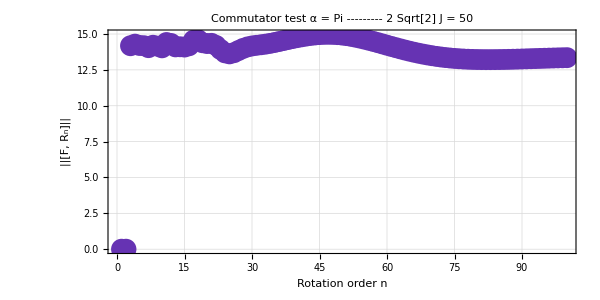

```mathematica
Print["Rotation order n    ||[F, Rn]||"];

ListPlot[commutatorResults,
  PlotStyle -> Directive[RGBColor[0.4, 0.2, 0.7], PointSize[0.025]],
  FrameLabel -> {Style["Rotation order n", 18, Black], Style["||[F, Rₙ]||", 18, Black]},
  PlotLabel -> Style["Commutator test  α = " <> ToString[NumberForm[alphaTest, {6,5}]] <>
                     "  J = " <> ToString[J], 15, Black],
  Frame -> True, Axes -> False, GridLines -> Automatic,
  ImageSize -> 600, AspectRatio -> 0.5]
```

```mathematica
(* ── Free parameters ── *)
alphaObs1 = 1.11;
alphaObs2 = 2.02;

(* ── Generate candidate expressions ── *)
candidates = DeleteDuplicates @ SortBy[Flatten @ {
  Table[Pi * p/q,       {p, 1, 6},  {q, 2, 15}],
  Table[Pi / Sqrt[n],   {n, 2, 15}],
  Table[Pi / (p + 1/q), {p, 1, 4},  {q, 2, 8}],
  Table[2 Pi * p/q,     {p, 1, 5},  {q, 5, 20}],
  Table[ArcCos[p/q],    {p, 0, 5},  {q, 2, 10}],
  Table[ArcTan[p/q],    {p, 1, 6},  {q, 1, 6}]
}, N[#] &];

(* ── Rank by proximity ── *)
ranked1 = SortBy[{N[#], Abs[N[#] - alphaObs1]} & /@ candidates, Last];
ranked2 = SortBy[{N[#], Abs[N[#] - alphaObs2]} & /@ candidates, Last];

Print["=== Top 10 candidates for α₁ ≈ ", alphaObs1, " ==="];
Print[TableForm[Take[ranked1, 10], TableHeadings -> {None, {"Value", "|residual|"}}]];

Print["=== Top 10 candidates for α₂ ≈ ", alphaObs2, " ==="];
Print[TableForm[Take[ranked2, 10], TableHeadings -> {None, {"Value", "|residual|"}}]];

(* ── Arithmetic relations between the two values ── *)
Print["\nDiagnostic ratios:"];
Print["α₂ / α₁          = ", N[alphaObs2 / alphaObs1, 10]];
Print["α₁ + α₂          = ", N[alphaObs1 + alphaObs2, 10]];
Print["2π - (α₁ + α₂)   = ", N[2 Pi - alphaObs1 - alphaObs2, 10]];
Print["π - α₁            = ", N[Pi - alphaObs1, 10]];
Print["π - α₂            = ", N[Pi - alphaObs2, 10]];
Print["α₂ - α₁           = ", N[alphaObs2 - alphaObs1, 10]];
```

=== Top 10 candidates for α₁ ≈ 1.11 ===

Value | |residual|
1.11024 | 0.000242335
1.11072 | 0.000720735
1.1088 | 0.00120259
1.10715 | 0.00285128
1.122 | 0.0119974
1.12789 | 0.0178853
1.1424 | 0.0323973
1.15928 | 0.0492795
1.0472 | 0.0628024
1.1781 | 0.0680972

=== Top 10 candidates for α₂ ≈ 2.02 ===

Value | |residual|
1.9635 | 0.0565046
2.0944 | 0.0743951
1.93329 | 0.0867122
1.88496 | 0.135044
1.848 | 0.172004
2.22144 | 0.201441
1.8138 | 0.206201
2.24399 | 0.223995
1.7952 | 0.224804
2.28479 | 0.264795

Diagnostic ratios:

α₂ / α₁          = 1.81982

α₁ + α₂          = 3.13

2π - (α₁ + α₂)   = 3.15319

π - α₁            = 2.03159

π - α₂            = 1.12159

α₂ - α₁           = 0.91

# Majorana constellation

```mathematica
(* Components of |θ,φ⟩ in the |S,m⟩ basis, m = -S,...,S  [Eq. 2.5] *)
CoherentStateSpin[S_,θ_,φ_]:=Table[Sqrt[Binomial[2S,S+m]]*If[S+m==0,1,Sin[θ/2]^(S+m)]*If[S-m==0,1,Cos[θ/2]^(S-m)]*Exp[-I(S+m) φ],{m,-S,S}]

(* Q(θ,φ) = |⟨θ,φ|ψ⟩|.b2  — state is a length-(2S+1) vector *)
HusimiQ[state_, S_, θ_, φ_] :=
  Abs[Conjugate[CoherentStateSpin[S, θ, φ]] . state]^2
```

```mathematica
(* Stellar polynomial f_ψ(z) [Eq. 2.9]; state[[k+1]] ↔ ψ_{k-S} *)
StellarFunction[state_, S_][z_] :=
  Sum[Sqrt[N[Binomial[2S, k], 50]] state[[k+1]] z^k, {k, 0, 2S}]

(* Majorana stars: roots of f_ψ in stereographic coordinates *)
MajoranaStars[state_,S_]:=Module[{hpState,poly},hpState=SetPrecision[state,30];
poly=Sum[Sqrt[Binomial[2S,k]] hpState[[k+1]] var^k,{k,0,2S}];
var/. NSolve[poly==0,var,WorkingPrecision->30]]

(* Reconstruct normalized state from stars in stereographic coords.
   Pass ComplexInfinity for any star located at the south pole. *)
StateFromStars[stars_, S_] :=
  Module[{finite, coeffs, state},
    finite  = DeleteCases[stars, _DirectedInfinity | ComplexInfinity];
    coeffs  = PadRight[
                CoefficientList[Expand[Product[z - s, {s, finite}]], z],
                2S + 1];
    state   = Table[coeffs[[k+1]] / Sqrt[N[Binomial[2S, k]]], {k, 0, 2S}];
    state / Norm[state]]

(* Stereographic ↔ Cartesian conversions [Eq. 2.3] *)
CartesianToStereo[{x_, y_, zc_}] :=
  If[Abs[1 + zc] < 1*^-10, ComplexInfinity, (x - I y)/(1 + zc)]

StereoToCartesian[z_] :=
  Module[{r2 = Abs[z]^2}, {2 Re[z], -2 Im[z], 1 - r2}/(1 + r2)]
```

```mathematica
(* Normalized unit-sphere vertices via Mathematica's built-in polyhedra *)
OctahedronVertices[]   := Normalize /@ N[PolyhedronData["Octahedron",   "VertexCoordinates"]]
IcosahedronVertices[]  := Normalize /@ N[PolyhedronData["Icosahedron",  "VertexCoordinates"]]
DodecahedronVertices[] := Normalize /@ N[PolyhedronData["Dodecahedron", "VertexCoordinates"]]

KingStateFromVertices[vertices_,S_]:=StateFromStars[CartesianToStereo/@SetPrecision[vertices,30],S]

(* Dispatch for S = 3, 6, 10 *)
KingState[3]  := KingStateFromVertices[OctahedronVertices[],   3]
KingState[6]  := KingStateFromVertices[IcosahedronVertices[],  6]
KingState[10] := KingStateFromVertices[DodecahedronVertices[], 10]
```

```mathematica
(* Pentagonal antiprism stars at latitude θ*, offset π/5 between rings *)
PentagonalAntiprismStars[θ_] :=
  Join[
    Table[{Sin[θ] Cos[2π k/5], Sin[θ] Sin[2π k/5],  Cos[θ]}, {k, 0, 4}],
    Table[{Sin[θ] Cos[2π k/5 + π/5], Sin[θ] Sin[2π k/5 + π/5], -Cos[θ]}, {k, 0, 4}]]

(* Multipole strength w_K for a given state [Eq. 4.7] — 
   numerical integration of Q against spherical harmonics *)
MultipoleStrength[state_, S_, K_] :=
  Sum[Abs[NIntegrate[
      HusimiQ[state, S, θ, φ] SphericalHarmonicY[K, q, θ, φ] Sin[θ],
      {θ, 0, π}, {φ, 0, 2π},
      Method -> "GlobalAdaptive", MaxRecursion -> 20]]^2,
    {q, -K, K}]
```

```mathematica
(* Optimize θ* so that w_1 through w_5 are simultaneously minimized *)
KingState[5] :=
  Module[{θopt},
    θopt = θ /. NMinimize[
      Sum[MultipoleStrength[
            KingStateFromVertices[PentagonalAntiprismStars[θ], 5], 5, K],
          {K, 1, 5}],
      {θ, 0.5, π/2}][[2]];
    KingStateFromVertices[PentagonalAntiprismStars[θopt], 5]]
```

```mathematica
(* Quick smoke tests *)
S = 3;
coh = CoherentStateSpin[S, Pi/3, Pi/4];
Print["Coherent state norm: ", Norm[coh] // N]

Print["Q at north pole: ", HusimiQ[coh, S, 0, 0] // N]

king3 = KingState[3];
Print["King S=3 norm: ", Norm[king3] // N]
Print["King S=3 vector: ", king3 // N]

stars3 = MajoranaStars[king3, 3];
Print["Majorana stars S=3: ", stars3]
```

Coherent state norm: 1.

Q at north pole: 0.177979

King S=3 norm: 1.

King S=3 vector: {0.,-0.707107,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.707107,0.}

Majorana stars S=3: {-1.,0,-1. ⅈ,1. ⅈ,1.}

```mathematica
MultipoleStrengthFast[state_, S_, K_] :=
  Sum[Abs[
    Sum[Conjugate[state[[S+m+1]]] state[[S+(m-Q)+1]] *
        ClebschGordan[{S, m-Q}, {K, Q}, {S, m}],
        {m, Max[-S, -S+Q], Min[S, S+Q]}]]^2,
    {Q, -K, K}]

KingState[5] := Module[{θopt},
  θopt = θ /. Last[NMinimize[
    Total[MultipoleStrengthFast[
        KingStateFromVertices[PentagonalAntiprismStars[θ], 5], 5, #] & /@ Range[1, 5]],
    {θ, π/6, π/2}]];
  KingStateFromVertices[PentagonalAntiprismStars[θopt], 5]]
```

```mathematica
king3=KingState[3];king5=KingState[5];
sVals={3,5,6,10};
```

```mathematica
king6=KingState[6];king10=KingState[10];
states={king3,king5,king6,king10};
```

```mathematica
HusimiPanel[state_, S_] :=
  Module[{nθ = 120, nφ = 240, grid},
    grid = Table[HusimiQ[state, S, θ, φ],
      {θ, π/nθ, π - π/nθ, π/nθ},
      {φ, 0, 2π - 2π/nφ, 2π/nφ}];
    ArrayPlot[grid,
      ColorFunction -> (Blend[{Blue, Cyan, Yellow, Red}, #] &),
      ColorFunctionScaling -> True,
      DataReversed -> {True, False},
      Frame -> True,
      FrameTicks -> {
        {{{1, "0"}, {nθ/2, "π/2"}, {nθ, "π"}}, None},
        {{{1, "0"}, {nφ/2, "π"}, {nφ, "2π"}}, None}},
      PlotLabel -> Style["S = " <> ToString[S], Bold, 14],
      ImageSize -> 280]]

ConstellationPanel[state_, S_] :=
  Module[{pts, hull},
    pts = Re[StereoToCartesian /@ MajoranaStars[state, S]];
    hull = ConvexHullMesh[pts];
    Show[
      Graphics3D[{
        EdgeForm[{Darker[Brown], Thin}],
        FaceForm[{RGBColor[0.9, 0.72, 0.15], Specularity[White, 40]}],
        hull,
        Black, Sphere[#, 0.07] & /@ pts}],
      Boxed -> False, Lighting -> "Standard",
      ViewPoint -> {1.5, 1.5, 2},
      ImageSize -> 280]]
```

```mathematica
GraphicsGrid[{
  MapThread[ConstellationPanel, {states, sVals}],
  MapThread[HusimiPanel,        {states, sVals}]},
  Spacings -> {10, 5},
  ImageSize -> Large]
```